```mathematica
v="9";
p="0.1";
ngap="4";
nvel="4";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
gap10v9=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
gap50v9=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
ga10k1=gap10v9[[All,1]];
ga50k1=gap50v9[[All,1]];
ga10k2=gap10v9[[All,2]];
ga50k2=gap50v9[[All,2]];
```

```mathematica
ga10k1=gap10v10[[All,1]];
ga50k1=gap50v10[[All,1]];
ga10k2=gap10v10[[All,2]];
ga50k2=gap50v10[[All,2]];
```

-7301.43  = val

0.07  = d0

1.  = α

1.  = z

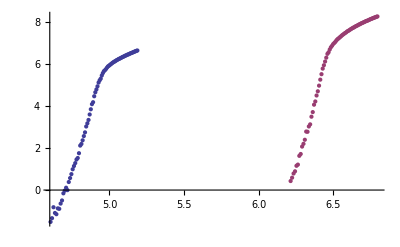

```mathematica
val=1000;
For[d0=0.07,d0<=0.08,d0+=0.001,
For[α=0.01,α<=1,α+=0.01,
z=α;
j=1;
While[ga10k1[[j]]<=d0,j++];
k=1;
While[ga50k1[[k]]<=d0,k++];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[10*1000.],
Log[ga10k2[[i]]]+α*Log[10*1000.]},{i,j,Length[ga10k1]-1}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[50*1000.],Log[ga50k2[[i]]]+α*Log[50*1000.]},{i,k,Length[ga50k1]-1}];
i10=Interpolation[g10k];
i50=Interpolation[g50k];
min=Max[Log[ga10k1[[j]]-d0]+z*Log[10*1000.],Log[ga50k1[[k]]-d0]+z*Log[50*1000.]];
max=Min[Log[ga10k1[[Length[ga10k1]-1]]-d0]+z*Log[10*1000.],Log[ga50k1[[Length[ga10k1]-1]]-d0]+z*Log[50*1000.]];
delta=(max-min)/50;
int=Sum[delta*(Max[i10[min+k*delta],i50[min+k*delta]]-Min[i10[min+k*delta],i50[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
d0f=d0;
αf=α;
zf=z;]

]
]

" = val"  val
" = d0" d0f
" = α" αf
" = z" zf
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[10*1000.],
Log[ga10k2[[i]]]+αf*Log[10*1000.]},{i,1,Length[ga10k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[50*1000.],Log[ga50k2[[i]]]+αf*Log[50*1000.]},{i,1,Length[ga50k1]}];
ListPlot[{g10k,g50k}]
```

0.0628811  = val

0.063  = d0

0.02  = α

0.02  = z

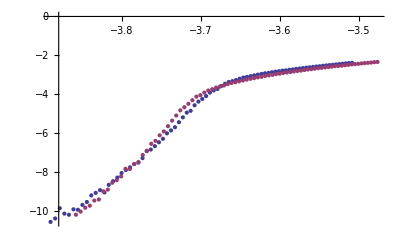

```mathematica
ga10k1=gap10v9[[All,1]];
ga50k1=gap50v9[[All,1]];
ga10k2=gap10v9[[All,2]];
ga50k2=gap50v9[[All,2]];
n1=10;
n2=50;
val=1000;
For[d0=0.063,d0<=0.068,d0+=0.0005,
For[α=0.01,α≤0.2,α+=0.01,
z=α;
j=1;
While[ga10k1[[j]]<=d0,j++];
k=1;
While[ga50k1[[k]]<=d0,k++];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[n1*1000.],
Log[ga10k2[[i]]]+α*Log[n1*1000.]},{i,j,Length[ga10k1]-1}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[n2*1000.],Log[ga50k2[[i]]]+α*Log[n2*1000.]},{i,k,Length[ga50k1]-1}];
i10=Interpolation[g10k];
i50=Interpolation[g50k];
min=Max[Log[ga10k1[[j]]-d0]+z*Log[n1*1000.],Log[ga50k1[[k]]-d0]+z*Log[n2*1000.]];
max=Min[Log[ga10k1[[Length[ga10k1]-1]]-d0]+z*Log[n1*1000.],Log[ga50k1[[Length[ga50k1]-1]]-d0]+z*Log[n2*1000.]];
delta=(max-min)/50;
int=Sum[delta*(Max[i10[min+k*delta],i50[min+k*delta]]-Min[i10[min+k*delta],i50[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
d0f=d0;
αf=α;
zf=z;]

]
]


" = val"  val
" = d0" d0f
" = α" αf
" = z" zf
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[n1*1000.],
Log[ga10k2[[i]]]+αf*Log[n1*1000.]},{i,1,Length[ga10k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[n2*1000.],Log[ga50k2[[i]]]+αf*Log[n2*1000.]},{i,1,Length[ga50k1]}];
ListPlot[{g10k,g50k}]
```

-1.58002×10^7  = val

0

1.  = α

1.  = z

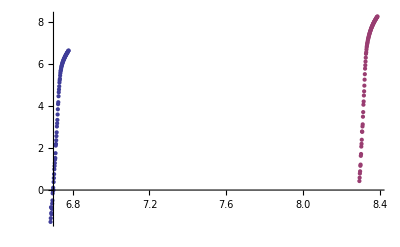

```mathematica
ga10k1=gap10v9[[All,1]];
ga50k1=gap50v9[[All,1]];
ga10k2=gap10v9[[All,2]];
ga50k2=gap50v9[[All,2]];
n1=10;
n2=50;
val=1000;
d0=0;
For[α=0.01,α≤1,α+=0.01,
z=α;
j=1;
While[ga10k1[[j]]<=d0,j++];
k=1;
While[ga50k1[[k]]<=d0,k++];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[n1*1000.],
Log[ga10k2[[i]]]+α*Log[n1*1000.]},{i,j,Length[ga10k1]-1}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[n2*1000.],Log[ga50k2[[i]]]+α*Log[n2*1000.]},{i,k,Length[ga50k1]-1}];
i10=Interpolation[g10k];
i50=Interpolation[g50k];
min=Max[Log[ga10k1[[j]]-d0]+z*Log[n1*1000.],Log[ga50k1[[k]]-d0]+z*Log[n2*1000.]];
max=Min[Log[ga10k1[[Length[ga10k1]-1]]-d0]+z*Log[n1*1000.],Log[ga50k1[[Length[ga50k1]-1]]-d0]+z*Log[n2*1000.]];
delta=(max-min)/50;
int=Sum[delta*(Max[i10[min+k*delta],i50[min+k*delta]]-Min[i10[min+k*delta],i50[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
d0f=d0;
αf=α;
zf=z;]

]


" = val"  val
" = d0" d0f
" = α" αf
" = z" zf
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[n1*1000.],
Log[ga10k2[[i]]]+αf*Log[n1*1000.]},{i,1,Length[ga10k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[n2*1000.],Log[ga50k2[[i]]]+αf*Log[n2*1000.]},{i,1,Length[ga50k1]}];
ListPlot[{g10k,g50k}]
```

0

- = α

0

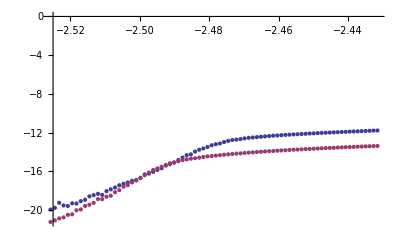

```mathematica
d0f=0;
αf=-1;
zf=0;
" = d0" d0f
" = α" αf
" = z" zf
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[n1*1000.],
Log[ga10k2[[i]]]+αf*Log[n1*1000.]},{i,1,Length[ga10k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[n2*1000.],Log[ga50k2[[i]]]+αf*Log[n2*1000.]},{i,1,Length[ga50k1]}];
ListPlot[{g10k,g50k}]
```